```mathematica
test=Import@FileNameJoin@{NotebookDirectory[],"../../Laboratories/electric transport/2025-04-16_cooling_from_150K_to_2K_VdP_I36_V54_1uA_I46_V53_1uA.dat"};
```

```mathematica
Dimensions@test
```

{1930,30}

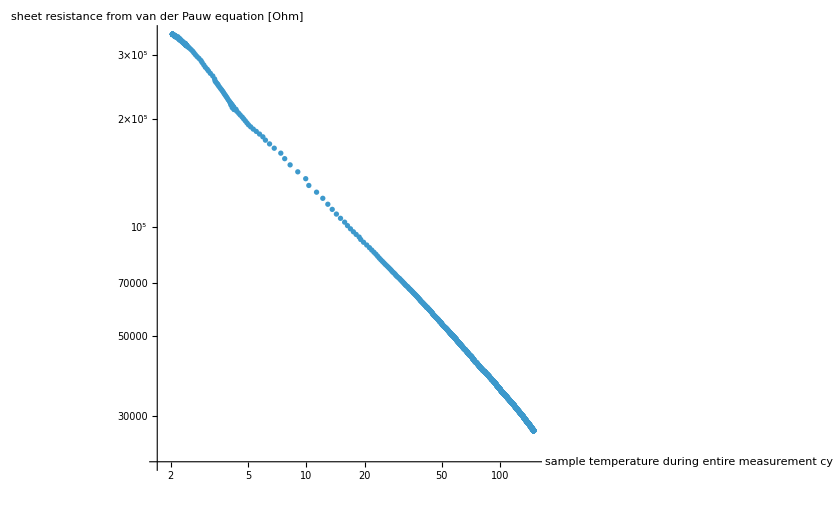

```mathematica
ListLogLogPlot[test[[All,{27,29}]],PlotRange->Full, AxesLabel->{"sample temperature during entire\nmeasurement cycle [Kelvin]", "sheet resistance from\nvan der Pauw equation [Ohm]"}]
```

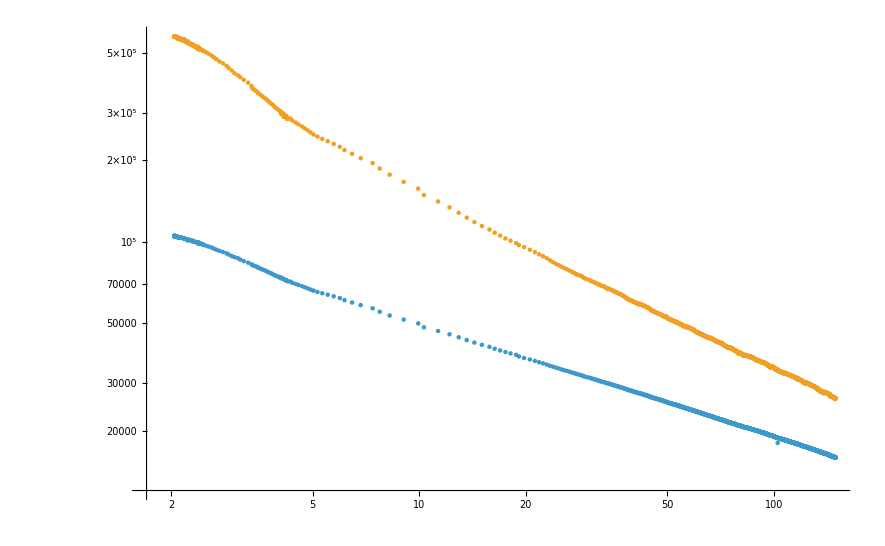

```mathematica
ListLogLogPlot[test[[All,{27,#}]]&/@{13,24},PlotRange->Full]
```

## Data

```mathematica
cooling150Kto2K=;
```

```mathematica
coolingRTto150K=;
```

```mathematica
HallEffect10K=;
```

```mathematica
magnetoresistance2K=;
```

```mathematica
resistance4to50=;
```

```mathematica
resistance10to3=;
```

```mathematica
resistance50to300=;
```

Column 1 : counts from last save
Column 2 : counts from measurement start
Column 3 : time from measurement start during FRONT measurement [seconds]
Column 4 : ignore
Column 5 : ignore
Column 6 : sample temperature during FRONT measurement [Kelvin]
Column 7 : temperature fluctuation during FRONT measurement [Kelvin]
Column 8 : resistance during FRONT measurement [Ohm]
Column 9 : average four - wire voltage during FRONT measurement [Volt]
Column 10 : positive four - wire voltage during FRONT measurement [Volt]
Column 11 : negative four - wire voltage during FRONT measurement [Volt]
Column 12 : excitation current during FRONT measurements [Ampere]
Column 13 : two - wire resistance during FRONT measurement [Ohm]
Column 14 : time from measurement start during BACK measurement [seconds]
Column 15 : ignore
Column 16 : ignore
Column 17 : sample temperature during BACK measurement [Kelvin]
Column 18 : temperature fluctuation during BACK measurement [Kelvin]
Column 19 : resistance during BACK measurement [Ohm]
Column 20 : average four - wire voltage during BACK measurement [Volt]
Column 21 : positive four - wire voltage during BACK measurement [Volt]
Column 22 : negative four - wire voltage during BACK measurement [Volt]
Column 23 : excitation current during BACK measurements [Ampere]
Column 24 : two - wire resistance during BACK measurement [Ohm]
Column 25 : ignore
Column 26 : ignore
Column 27 : sample temperature during entire measurement cycle [Kelvin]
Column 28 : temperature fluctuation during entire measurement cycle [Kelvin]
Column 29 : sheet resistance from van der Pauw equation [Ohm]
Column 30 : applied magnetic field [Tesla]; ONLY IF MANUALLY RECORDED IN THE CONTROL PROGRAM!

## Resistivity

We need to use the following data:
• <10K during cooling
• >10K during warm-up

```mathematica
Dimensions@resistance50to300[[All,30]]
```

{4527}

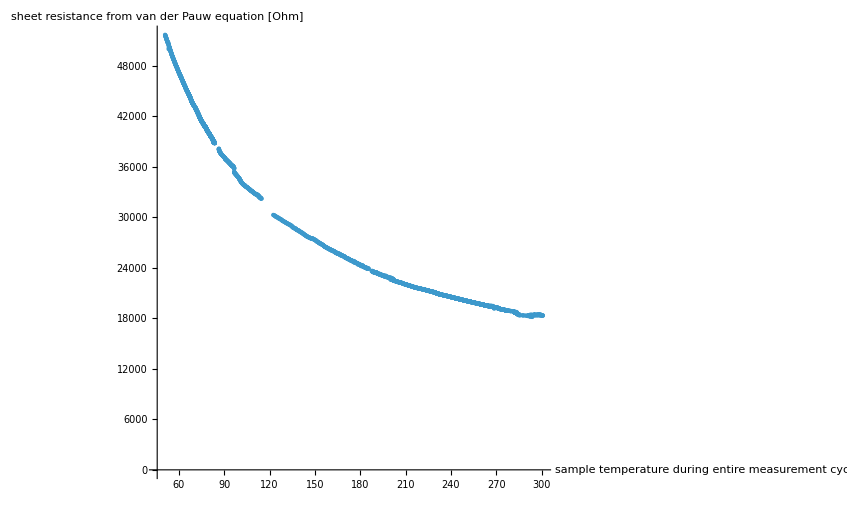

```mathematica
ListPlot[resistance50to300[[All,{27,29}]],AxesLabel->{ "sample temperature during\nentire measurement cycle [Kelvin]","sheet resistance from\nvan der Pauw equation [Ohm]"}]
```

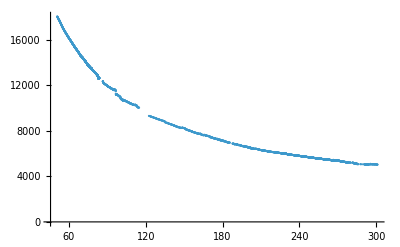

```mathematica
ListPlot@resistance50to300[[All,{27,19}]]
```

```mathematica
Ra=resistance50to300[[All,19]];
Rb=resistance50to300[[All,8]];
VanDerPauw=Table[NSolveValues[Log[Exp[-π Ra[[i]]/Rs]+Exp[-π Rb[[i]]/Rs]]==0,Rs,Reals][[1]],{i,1,Length@Ra}];
```

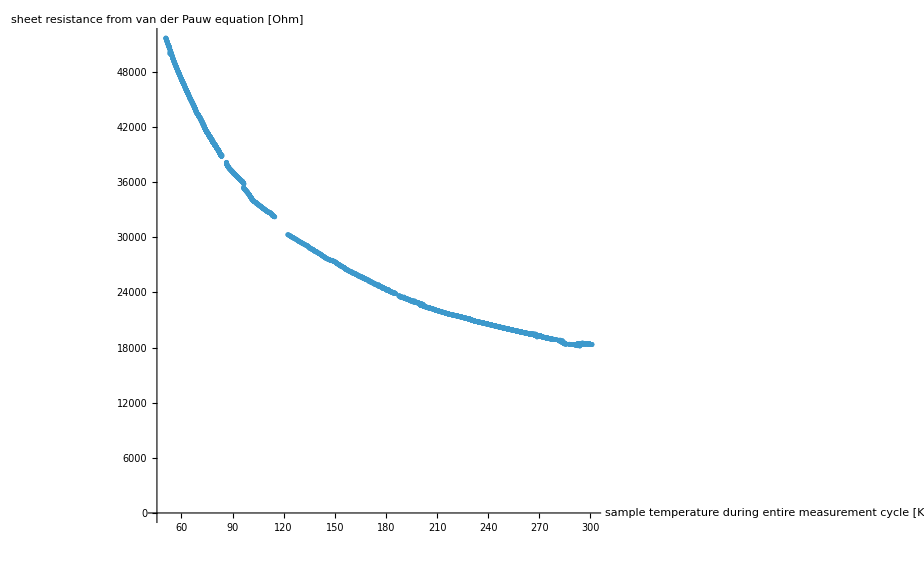

```mathematica
Show[
ListPlot[resistance50to300[[All,{27,29}]],AxesLabel->{ "sample temperature during\nentire measurement cycle [Kelvin]","sheet resistance from\nvan der Pauw equation [Ohm]"}],
ListPlot[Transpose@{resistance50to300[[All,27]],VanDerPauw}]
]
```

Check that I get the same solutions to the Van der Pauw equations that the software did.

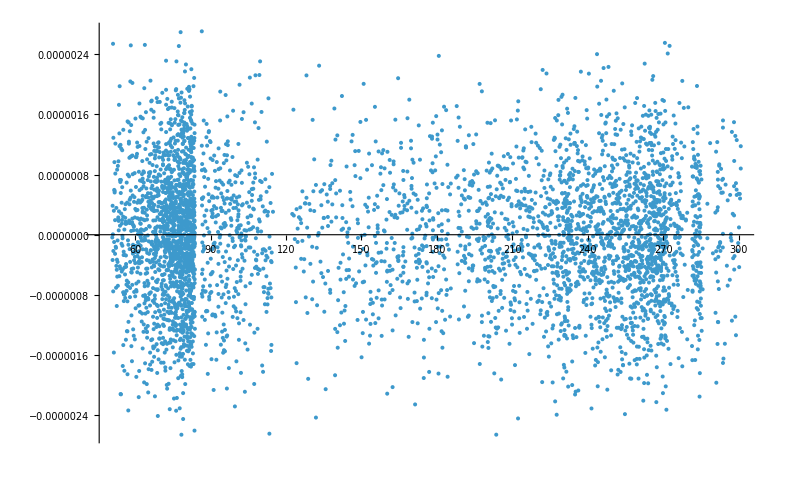

```mathematica
ListPlot[Transpose@{resistance50to300[[All,27]],VanDerPauw-resistance50to300[[All,29]]}]
```